## Chapter 13 & 17 [Complex Numbers & Functions, Conformal Mapping]

## 13/17.1 Complex Numbers, Polar Form, Plotting

```mathematica
Clear["Global`*"]
```

```mathematica
z1=3+4I
```

3+4 ⅈ

```mathematica
z2=5-2I
```

5-2 ⅈ

```mathematica
z1+z2
```

8+2 ⅈ

```mathematica
z1-z2
```

-2+6 ⅈ

```mathematica
z1 z2
```

23+14 ⅈ

```mathematica
z1/z2
```

7/29+(26 ⅈ)/29

```mathematica
N[%]
```

0.241379+0.896552 ⅈ

```mathematica
(3.0+4I)/(5-2I)
```

0.241379+0.896552 ⅈ

```mathematica
Cos[3+I]
```

Cos[3+ⅈ]

```mathematica
ComplexExpand[%]
```

Cos[3] Cosh[1]-ⅈ Sin[3] Sinh[1]

```mathematica
Cos[3.0+I]
```

-1.52764-0.165844 ⅈ

```mathematica
z=16-12I
```

16-12 ⅈ

```mathematica
Re[z]
```

16

```mathematica
Im[z]
```

-12

```mathematica
Abs[z]
```

20

```mathematica
Arg[z]
```

-ArcTan[3/4]

```mathematica
N[%]
```

-0.643501

```mathematica
Conjugate[z]
```

16+12 ⅈ

```mathematica
Re[Cos[3+I]]
```

Re[Cos[3+ⅈ]]

```mathematica
ComplexExpand[%]
```

Cos[3] Cosh[1]

```mathematica
N[%]
```

-1.52764

```mathematica
ComplexExpand[Im[Cos[3+I]]]
```

-Sin[3] Sinh[1]

```mathematica
Abs[ComplexExpand[Cos[3+I]]]
```

√(Cos[3]^2 Cosh[1]^2+Sin[3]^2 Sinh[1]^2)

```mathematica
Conjugate[-4.8+0.3I]
```

-4.8-0.3 ⅈ

```mathematica
z=x+I y
```

x+ⅈ y

```mathematica
Conjugate[z]
```

Conjugate[x]-ⅈ Conjugate[y]

```mathematica
ComplexExpand[%]
```

x-ⅈ y

```mathematica
f=z^3
```

(x+ⅈ y)^3

```mathematica
Re[f]
```

Re[(x+ⅈ y)^3]

```mathematica
ComplexExpand[%]
```

x^3-3 x y^2

```mathematica
ComplexExpand[Im[f]]
```

3 x^2 y-y^3

```mathematica
Conjugate[f]
```

(Conjugate[x]-ⅈ Conjugate[y])^3

```mathematica
ComplexExpand[Conjugate[f]]
```

x^3-3 x y^2+ⅈ (-3 x^2 y+y^3)

```mathematica
fbar=f/.Complex[x_,y_]->Complex[x,-y]
```

(x-ⅈ y)^3

```mathematica
ComplexExpand[%]
```

x^3-3 x y^2+ⅈ (-3 x^2 y+y^3)

```mathematica
re=Simplify[(f+fbar)/2]
```

x^3-3 x y^2

```mathematica
im=Simplify[(f-fbar)/(2I)]
```

3 x^2 y-y^3

```mathematica
Simplify[absSquare=f fbar]
```

(x^2+y^2)^3

```mathematica
z=8+3I
```

8+3 ⅈ

```mathematica
Abs[z]Exp[I Arg[z]]
```

√73 ⅇ^(ⅈ ArcTan[3/8])

```mathematica
ComplexExpand[%]
```

8+3 ⅈ

```mathematica
Clear[z,f]
```

```mathematica
f[z_]=Abs[z]Exp[I Arg[z]]
```

ⅇ^(ⅈ Arg[z]) Abs[z]

```mathematica
f[1+I]
```

√2 ⅇ^((ⅈ π)/4)

```mathematica
f[10I]
```

10 ⅈ

```mathematica
f[-10]
```

-10

```mathematica
p[z_]:=Abs[z]Exp[HoldForm[Evaluate[I Arg[z]]]]
```

```mathematica
pol1=p[1+I]
```

√2 ⅇ^((ⅈ π)/4)

```mathematica
pol2=p[10I]
```

10 ⅇ^((ⅈ π)/2)

```mathematica
pol3=p[-10]
```

10 ⅇ^(ⅈ π)

```mathematica
ComplexExpand[ReleaseHold[pol1]]
```

1+ⅈ

```mathematica
ComplexExpand[ReleaseHold[pol2]]
```

10 ⅈ

```mathematica
ComplexExpand[ReleaseHold[pol3]]
```

-10

```mathematica
Simplify[Abs[r]Exp[I t]Abs[p]Exp[I s]]
```

ⅇ^(ⅈ (s+t)) Abs[p] Abs[r]

```mathematica
P1=ListPlot[{{5,2},{5,-2}},PlotRange->{{0,6},{-3,3}},Prolog->AbsolutePointSize[4]]
```

-Graphics-

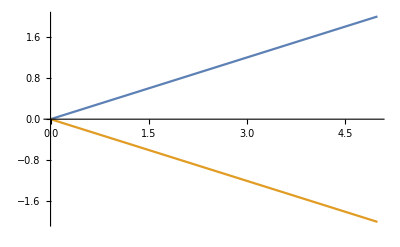

```mathematica
P2=Plot[{(2/5)x,-(2/5)x},{x,0,5}]
```

```mathematica
Show[P1,P2]
```

-Graphics-

## 13/17.2 Equations, Roots, Sets in the Complex Plane

```mathematica
Clear[z]
```

```mathematica
eq=z^2-(5+I)z+8+I==0
```

(8+ⅈ)-(5+ⅈ) z+z^2==0

```mathematica
sol=Solve[eq,z]
```

{{z→2-ⅈ},{z→3+2 ⅈ}}

```mathematica
sol[[1,1,2]]
```

2-ⅈ

```mathematica
sol[[2,1,2]]
```

3+2 ⅈ

```mathematica
FindRoot[eq,{z,2.5}]
```

{z→2.-1. ⅈ}

```mathematica
FindRoot[eq,{z,4+I}]
```

{z→3.+2. ⅈ}

```mathematica
Clear[z,sol,n]
```

```mathematica
sol=Solve[z^9==1.0,z]
```

{{z→-0.939693-0.34202 ⅈ},{z→-0.939693+0.34202 ⅈ},{z→-0.5-0.866025 ⅈ},{z→-0.5+0.866025 ⅈ},{z→0.173648-0.984808 ⅈ},{z→0.173648+0.984808 ⅈ},{z→0.766044-0.642788 ⅈ},{z→0.766044+0.642788 ⅈ},{z→1.}}

```mathematica
S=Table[{Re[sol[[n,1,2]]],Im[sol[[n,1,2]]]},{n,1,9}]
```

{{-0.939693,-0.34202},{-0.939693,0.34202},{-0.5,-0.866025},{-0.5,0.866025},{0.173648,-0.984808},{0.173648,0.984808},{0.766044,-0.642788},{0.766044,0.642788},{1.,0}}

```mathematica
P1=ListPlot[S,Prolog->AbsolutePointSize[4]];
```

```mathematica
P2=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
```

```mathematica
Show[P1,P2,AspectRatio->Automatic,PlotRange->{-1,1}]
```

-Graphics-

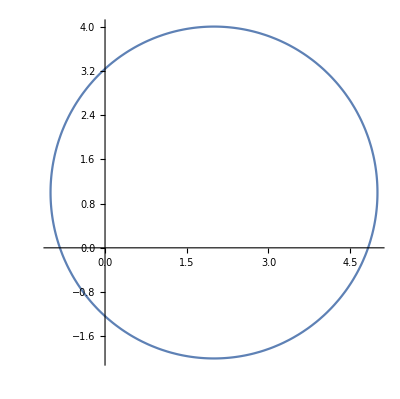

```mathematica
P3=ParametricPlot[{2+3Cos[t],1+3Sin[t]},{t,0,2Pi},AspectRatio->Automatic]
```

```mathematica
P4=ParametricPlot[{2+1.4Cos[t],1+1.4Sin[t]},{t,0,2Pi}];
```

```mathematica
P5=ListPlot[{{2,1}}];
```

```mathematica
Show[P3,P4,P5,Prolog->AbsolutePointSize[4]]
```

-Graphics-

## 13/17.3 Cauchy-Riemann Equations, Harmonic Functions

```mathematica
Clear[f,x,y,u,v]
```

```mathematica
f=Exp[x](Cos[y]+I Sin[y])
```

ⅇ^x (Cos[y]+ⅈ Sin[y])

```mathematica
Re[f]
```

Re[ⅇ^x (Cos[y]+ⅈ Sin[y])]

```mathematica
u=ComplexExpand[Re[f]]
```

ⅇ^x Cos[y]

```mathematica
v=ComplexExpand[Im[f]]
```

ⅇ^x Sin[y]

```mathematica
ux=D[u,x]
```

ⅇ^x Cos[y]

```mathematica
vy=D[v,y]
```

ⅇ^x Cos[y]

```mathematica
CR2=D[u,y]+D[v,x]
```

0

```mathematica
f2=x^2+y^2
```

x^2+y^2

```mathematica
D[ComplexExpand[Re[f2]],x]-D[ComplexExpand[Im[f2]],y]
```

2 x

```mathematica
Clear[x,y,z,h]
```

```mathematica
u=x^2-y^2-y
```

x^2-y-y^2

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
SetCoordinates[Cartesian[x,y,zeta]]
```

Cartesian[x,y,zeta]

```mathematica
Laplacian[u]
```

0

```mathematica
ux=D[u,x]
```

2 x

```mathematica
v=Integrate[ux,y]+h[x]
```

2 x y+h[x]

```mathematica
vx=D[v,x]==-D[u,y]
```

2 y+h'[x]==1+2 y

```mathematica
v=Integrate[vx[[2]],x]+c
```

c+x (1+2 y)

```mathematica
f=u+I v
```

x^2-y-y^2+ⅈ (c+x (1+2 y))

```mathematica
f/.{x->(z+Conjugate[z])/2,y->{z-Conjugate[z]}/(2I)}
```

{1/2 ⅈ (z-Conjugate[z])+1/4 (z-Conjugate[z])^2+1/4 (z+Conjugate[z])^2+ⅈ (c+1/2 (1-ⅈ (z-Conjugate[z])) (z+Conjugate[z]))}

```mathematica
Simplify[%]
```

{ⅈ c+z (ⅈ+z)}

## 13/17.4 Conformal Mapping

```mathematica
w[x_,y_]:=(1+I)(x+I y)
```

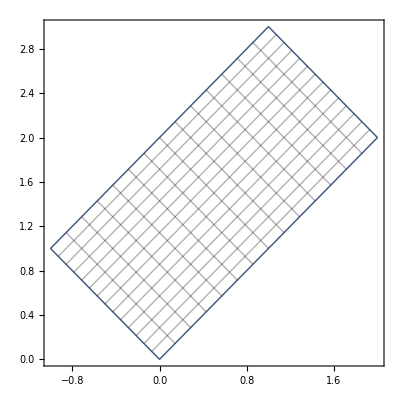

```mathematica
P1=ParametricPlot[Through[{Re,Im}[w[x,y]]],{x,0,2},{y,0,1},PlotStyle->None,Mesh->Full]
```

```mathematica
w[x_,y_]:=(x+I y)^2
```

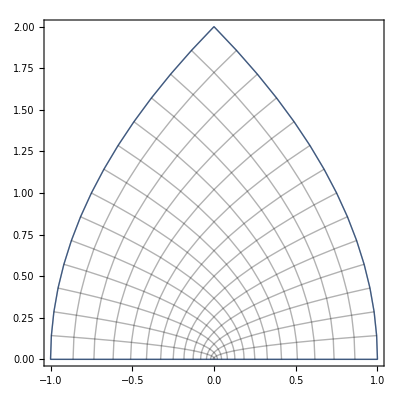

```mathematica
P2=ParametricPlot[Through[{Re,Im}[w[x,y]]],{x,0,1},{y,0,1},PlotStyle->None,Mesh->Full]
```

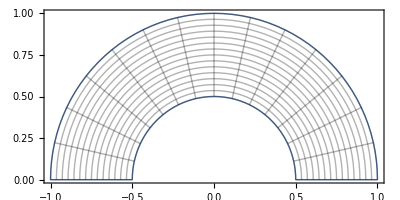

```mathematica
P3=ParametricPlot[Through[{Re,Im}[Identity[r Exp[I t]]]], {r, 1/2, 1}, {t,0,Pi},PlotStyle->None,Mesh->Full]
```

```mathematica
w[r_,t_]:=1/(r Exp[I t])
```

```mathematica
P4=ParametricPlot[Through[{Re,Im}[Identity[r Exp[I t]]]], {r, 1/2, 1}, {t,0,Pi/4},PlotStyle->None,Mesh->Full];
```

```mathematica
P5=ParametricPlot[Through[{Re,Im}[w[r,t]]], {r, 1/2, 1}, {t,0,Pi/4},PlotStyle->None,Mesh->Full];
```

```mathematica
P6=ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi}];
```

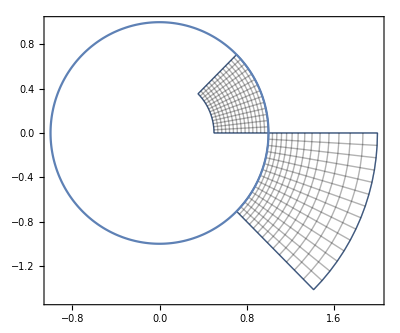

```mathematica
Show[{P4,P5,P6},PlotRange->{{-1,2},{-1.5,1}}]
```

```mathematica
w[r_,t_]:=(r Exp[I t])+1/r Exp[I t]
```

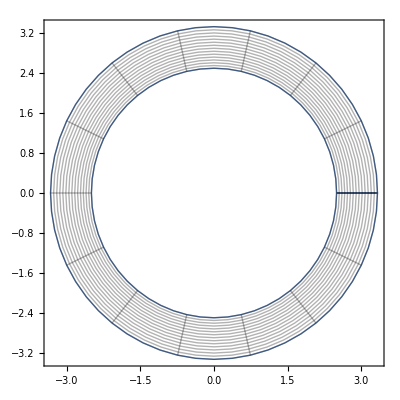

```mathematica
P7=ParametricPlot[Through[{Re,Im}[w[r,t]]], {r, 2,3}, {t,0,2Pi},PlotStyle->None,Mesh->Full]
```

```mathematica
z=1/10(1+I+Sqrt[122]Exp[I t])
```

1/10 ((1+ⅈ)+√122 ⅇ^(ⅈ t))

```mathematica
w=z+1/z
```

10/((1+ⅈ)+√122 ⅇ^(ⅈ t))+1/10 ((1+ⅈ)+√122 ⅇ^(ⅈ t))

```mathematica
Simplify[ComplexExpand[Re[w]]]
```

(173+113 √122 Cos[t]+61 Cos[2 t]+√122 Sin[t]+61 Sin[2 t])/(10 (62+√122 Cos[t]+√122 Sin[t]))

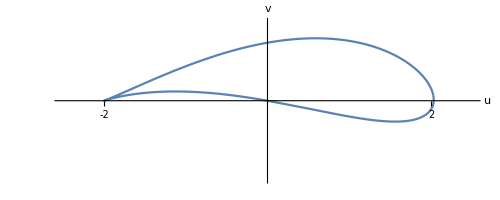

```mathematica
ParametricPlot[{Re[w],Im[w]},{t,0,2Pi},AspectRatio->Automatic,PlotRange->{{-2.5,2.5},{-0.5,0.5}},AxesLabel->{"u","v"},Ticks->{{-2,2},None}]
```

## 13/17.5 Exponential, Trigonometric & Hyperbolic Functions

```mathematica
Clear[z,x,y]
```

```mathematica
f=-5 z^3+(12-2I)z^2-I z-200
```

-200-ⅈ z+(12-2 ⅈ) z^2-5 z^3

```mathematica
f/.z->2+3I
```

-3+107 ⅈ

```mathematica
z=x+I y
```

x+ⅈ y

```mathematica
u=ComplexExpand[Re[f]]
```

-200+12 x^2-5 x^3+y+4 x y-12 y^2+15 x y^2

```mathematica
Plot3D[u,{x,0,5},{y,0,5},ViewPoint->{1.5,1,1}]
```

-Graphics3D-

```mathematica
Abs[f]/.z->2+3I
```

√11458

```mathematica
N[%]
```

107.042

```mathematica
Clear[z]
```

```mathematica
D[f,z]
```

-ⅈ+(24-4 ⅈ) z-15 z^2

```mathematica
Exp[1.4-0.6I]
```

3.3469-2.28974 ⅈ

```mathematica
Exp[2+I]
```

ⅇ^(2+ⅈ)

```mathematica
ComplexExpand[%]
```

ⅇ^2 Cos[1]+ⅈ ⅇ^2 Sin[1]

```mathematica
Re[Exp[2+I]]
```

ⅇ^2 Cos[1]

```mathematica
N[Exp[2+I]]
```

3.99232+6.21768 ⅈ

```mathematica
N[Exp[1],50]
```

2.7182818284590452353602874713526624977572470937

```mathematica
ComplexExpand[Exp[I z]]
```

Cos[z]+ⅈ Sin[z]

```mathematica
z=x+I y
```

x+ⅈ y

```mathematica
ComplexExpand[Cos[z]]
```

Cos[x] Cosh[y]-ⅈ Sin[x] Sinh[y]

```mathematica
ComplexExpand[Sin[z]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

```mathematica
N[Cos[2+3I]]
```

-4.18963-9.10923 ⅈ

```mathematica
N[Tan[1+3I]]
```

0.00451714+1.00205 ⅈ

```mathematica
Plot3D[Abs[Sin[x+I y]],{x,0,2Pi},{y,0,2},ViewPoint->{-2,-3,1}]
```

-Graphics3D-

```mathematica
Clear[z,w]
```

```mathematica
w[x_,y_]:=Sin[x+I y]
```

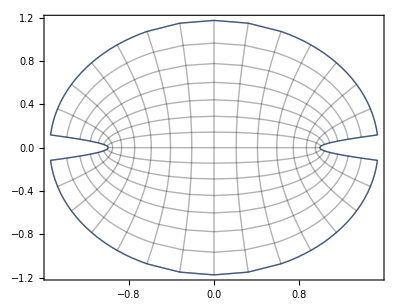

```mathematica
ParametricPlot[Through[{Re,Im}[w[x,y]]],{x,-Pi/2+0.1,Pi/2-0.1},{y,-1,1},PlotStyle->None,Mesh->Full]
```

```mathematica
Clear[z,w]
```

```mathematica
(Exp[I z]+Exp[-I z])/2
```

1/2 (ⅇ^(-ⅈ z)+ⅇ^(ⅈ z))

```mathematica
ComplexExpand[%]
```

Cos[z]

```mathematica
Cosh[I z]
```

Cos[z]

```mathematica
Cos[I z]
```

Cosh[z]

```mathematica
Simplify[Cosh[z]^2-Sinh[z]^2]
```

1

```mathematica
Tanh[1-2I]
```

-ⅈ Tan[2+ⅈ]

```mathematica
N[%]
```

1.16674+0.243458 ⅈ

```mathematica
h=ComplexExpand[Re[Tanh[x+I y]]]
```

Sinh[2 x]/(Cos[2 y]+Cosh[2 x])

```mathematica
h-Sinh[x]Cosh[x]/(Sinh[x]^2+Cos[y]^2)
```

-(Cosh[x] Sinh[x])/(Cos[y]^2+Sinh[x]^2)+Sinh[2 x]/(Cos[2 y]+Cosh[2 x])

```mathematica
Simplify[%]
```

0

## 13/17.6 Complex Logarithm

```mathematica
ComplexExpand[Log[x+I y]]
```

ⅈ Arg[x+ⅈ y]+1/2 Log[x^2+y^2]

```mathematica
Arg[x+I y]
```

Arg[x+ⅈ y]

```mathematica
ComplexExpand[Log[4-3I]]
```

-ⅈ ArcTan[3/4]+Log[5]

```mathematica
Re[Log[3-4I]]
```

Re[Log[3-4 ⅈ]]

```mathematica
ComplexExpand[%]
```

Log[5]

```mathematica
ComplexExpand[Im[Log[3-4I]]]
```

-ArcTan[4/3]

```mathematica
N[Log[3-4I]]
```

1.60944-0.927295 ⅈ

```mathematica
Log[-1]
```

ⅈ π

```mathematica
N[%,50]
```

3.1415926535897932384626433832795028841971693993751 ⅈ

```mathematica
D[Log[z],z]
```

1/z

```mathematica
L=Log[3-4I]+2n Pi I
```

2 ⅈ n π+Log[3-4 ⅈ]

```mathematica
S=Table[N[L],{n,-2,3}]
```

{1.60944-13.4937 ⅈ,1.60944-7.21048 ⅈ,1.60944-0.927295 ⅈ,1.60944+5.35589 ⅈ,1.60944+11.6391 ⅈ,1.60944+17.9223 ⅈ}

```mathematica
S2=Table[{Re[S[[n]]],Im[S[[n]]]},{n,1,6}]
```

{{1.60944,-13.4937},{1.60944,-7.21048},{1.60944,-0.927295},{1.60944,5.35589},{1.60944,11.6391},{1.60944,17.9223}}

```mathematica
ListPlot[S2,Prolog->AbsolutePointSize[4]]
```

-Graphics-

## ---------------------The End---------------------